-Graphics-

# Random Processes in Finance

## Michael Kelly

Wolfram Research, Inc.

http://www.wolfram.com/broadcast/video.php?c=324&v=633

## Outline

Wolfram Finance Platform has a comprehensive range of built-in random processes that can be used to represent many real-life random events and financial processes. Because of the wide range of such processes, it is not possible to cover all possibilities in this presentation. Instead we will look briefly at the list of such processes and concentrate on those aspects that would be of importance in the financial field. First, we describe the collection of processes that exist in Wolfram Finance Platform and how they are divided according to their discrete and continuous time and random states. Next, we give a more formal definition within the mathematical statistics context. Then we look at some visualizations and show how random variables can be obtained from random processes for both the univariate and multivariate cases. We consider time series processes such as exchange rates and show how they can be predicted. Then we look at how stochastic differential equations (SDEs) can be constructed by introducing noise into ordinary differential equations (ODEs). The canonical random process is the Ito process. We consider examples of the Ito process and show how to generate simulations from their corresponding SDEs. Next, we consider in detail the financial geometric Brownian motion process that is used to describe the behavior of stock prices, and lastly we consider built-in processes that are used to describe interest rate models.

## Random Processes: Discrete and Continuous Time and Random States

If we allow both time and random events to vary, then we get a random process. Examples of discrete time and state processes include the Bernoulli, binomial, random walk, discrete Markov, compound Poisson, and compound renewal processes. Time series processes have discrete time but continuous states, queueing and renewal processes are continuous in time but discrete in their states, while processes that can be represented by SDEs are continuous in time and states:

```mathematica
ldd={BernoulliProcess,BinomialProcess,RandomWalkProcess,DiscreteMarkovProcess,CompoundPoissonProcess,CompoundRenewalProcess};
lcd={PoissonProcess,TelegraphProcess,ContinuousMarkovProcess,QueueingProcess,QueueingNetworkProcess,RenewalProcess,CompoundPoissonProcess,CompoundRenewalProcess};
ldc={MAProcess,ARProcess,ARMAProcess,ARIMAProcess,SARMAProcess,SARIMAProcess,FARIMAProcess,CompoundRenewalProcess};
lcc={WienerProcess,GeometricBrownianMotionProcess,BrownianBridgeProcess,OrnsteinUhlenbeckProcess,CoxIngersollRossProcess,FractionalBrownianMotionProcess,ItoProcess,StratonovichProcess,RenewalProcess,CompoundRenewalProcess};
ProcessListGrid[{{ldd,ldc},{lcd,lcc}}]//CellDisplay
```

| Discrete State | Continuous State
Discrete Time | BernoulliProcess
BinomialProcess
RandomWalkProcess
DiscreteMarkovProcess
CompoundPoissonProcess
CompoundRenewalProcess | MAProcess
ARProcess
ARMAProcess
ARIMAProcess
SARMAProcess
SARIMAProcess
FARIMAProcess
CompoundRenewalProcess
Continuous Time | PoissonProcess
TelegraphProcess
ContinuousMarkovProcess
QueueingProcess
QueueingNetworkProcess
RenewalProcess
CompoundPoissonProcess
CompoundRenewalProcess | WienerProcess
GeometricBrownianMotionProcess
BrownianBridgeProcess
OrnsteinUhlenbeckProcess
CoxIngersollRossProcess
FractionalBrownianMotionProcess
ItoProcess
StratonovichProcess
RenewalProcess
CompoundRenewalProcess

Here we show the graphical representation of some of the above processes:

```mathematica
pcc=Plot3D[PDF[NormalDistribution[t,√t],x],{t,1,10},{x,-3 √10+5,3 √10+5},AxesLabel->Automatic,PlotRange->All,MeshFunctions->{#1&},Mesh->{Range[9]},PlotPoints->50];
pcd=Plot3D[Evaluate[PDF[PoissonDistribution[t],Floor[x-0.25]]Sum[UnitBox[2(x-i)],{i,0,10}]],{t,1,10},{x,-0.5,10.5},MeshFunctions->{#2&},Mesh->{Sort[Join[Range[0,10]-0.25,Range[0,10]+0.25]]},MeshShading->{None,Automatic},Exclusions->{Sin[π (x-0.25)],Sin[π (x+0.25)]},AxesLabel->Automatic,PlotRange->All,PlotPoints->75,BoundaryStyle->None,Ticks->{Automatic,Range[0,10,5],Automatic}];
pdc=Plot3D[Evaluate[PDF[MAProcess[{1,2},1][t],x]Sum[UnitBox[2(t-i)],{i,0,10}]],{t,-0.5,10.5},{x,-5,5},MeshFunctions->{#1&},Mesh->{Sort[Join[Range[0,10]-0.25,Range[0,10]+0.25]]},MeshShading->{None,Automatic},Exclusions->{Sin[π (t-0.25)],Sin[π (t+0.25)]},AxesLabel->Automatic,BoundaryStyle->None];
pdd=DiscretePlot3D[PDF[BinomialDistribution[t,2/3],x],{t,0,10},{x,0,10},ExtentSize->1/2,PlotStyle->EdgeForm[Opacity[0.3]],FillingStyle->Opacity[0.4],AxesLabel->Automatic];
With[{s=200},ProcessDefinitionGrid[{{Show[pdd,ImageSize->s],Show[pdc,ImageSize->s]},{Show[pcd,ImageSize->s],Show[pcc,ImageSize->s]}}]]//CellDisplay
```

| Discrete State | Continuous State
Discrete Time | -Graphics3D- | -Graphics3D-
Continuous Time | -Graphics3D- | -Graphics3D-

## What Are Random Processes and Random Variables?

Random processes are an important part of modern finance. Ever since the ground-breaking paper by Black and Scholes in 1973, it has been known that Ito processes and SDEs can be used as a counterpart to partial differential equations (PDEs) to describe financial stocks, bonds, interest rates, and derivatives of any of the previous instruments. The mathematical description of a random process X is a random function X[t,ω] that depends upon deterministic and random event domains. As such, random processes can be regarded as mappings from the cross space T×Ω into the value space S. Random variables are special cases of random processes. If we fix the first argument, then we get a mapping from the random event space Ω into the value space S. These mappings are displayed below. For the sake of convenience and because we are also concerned with looking at a range of financial time series, we will take the deterministic space to be time and the second space to be the set of all possible random events Ω. The value space can be single or multidimensional. In the instance where we are considering just one stock, we would have a time series of values, and for a portfolio we would consider a multidimensional space where each element is the time-associated vector of portfolio values.

Random variable (distribution): x:Ω→S gives value in S for each event ω∈Ω

Random function (process): x:T×Ω→S gives function T→S for each event ω∈Ω

## Visualization of Random Processes

It is a simple matter to take any of the above processes and use Wolfram Finance Platform’s vast array of plotting and graphing functions to visually represent any of them. The built-in RandomFunction allows one to generate random values for any of the defined processes:

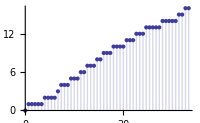
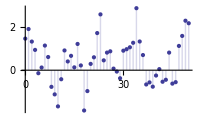
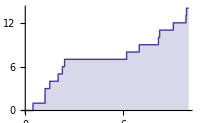
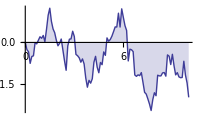
| Discrete State | Continuous State
Discrete Time | -Graphics- | -Graphics-
Continuous Time | -Graphics- | -Graphics-

```mathematica
SeedRandom[1234];
gdd=ListPlot[RandomFunction[BinomialProcess[1/4],{0,50}],Filling->Axis];
gcd=ListLinePlot[RandomFunction[PoissonProcess[1],{0,10}],Filling->Axis,InterpolationOrder->0,Ticks->{Automatic,Range[0,14,2]}];
gdc=ListPlot[RandomFunction[ARProcess[{0.7},1],{0,50}],Filling->Axis,AxesOrigin->{0,0}];
gcc=ListLinePlot[RandomFunction[WienerProcess[],{0,10,0.1}],Filling->Axis,AxesOrigin->{0,0}];
With[{s=200},ProcessDefinitionGrid[{{Show[gdd,ImageSize->s],Show[gdc,ImageSize->s]},{Show[gcd,ImageSize->s],Show[gcc,ImageSize->s]}}]]//CellDisplay
```

As an example, consider the trajectory of a small particle suspended in fluid:

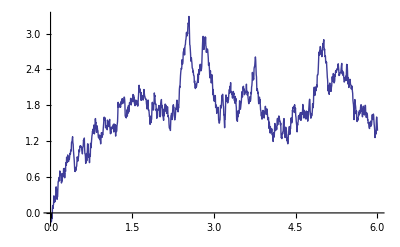

```mathematica
ListLinePlot[RandomFunction[WienerProcess[],{0,6,0.005}]]
```

Experiencing jolts of random intensity at random times, the position of the particle can be viewed as a random process.

## Random Variables Obtained from Random Processes

If we fix the time component t=t_1 in a process X[t_1, ω], then we have a time slice of the process that is a random variable that can take a range of values and has a probability distribution. Wolfram Finance Platform has a wide range of functions and statistical operators that it can apply to all such distributions.

Here are some examples that show slices of a random process at any fixed time resulting in a distribution.

### Process at a given time

If we were to repeat our experiment, trajectories would be different:

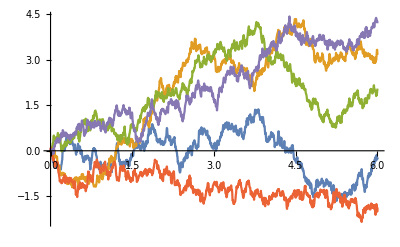

```mathematica
ListLinePlot[RandomFunction[WienerProcess[],{0,6,0.005},5]]
```

Thus the value of process at any given time is a random variable:

```mathematica
proc=WienerProcess[];
```

```mathematica
proc[t]
```

NormalDistribution[0,√t]

The values of the process at different times are, generically speaking, dependent random variables:

```mathematica
proc[{Subscript[t, 1],Subscript[t, 2]}]
```

BinormalDistribution[{0,0},{√t_1,√t_2},√(t_1/t_2)]

### Univariate examples

Univariate slice distributions (marginals):

Distributions: x[ω] is a random variable (distribution), x[ω_1] a number.

Processes: x[t,ω] is a random function (process), x[t_1,ω] a random variable (distribution), x[t,ω_1] a function, x[t_1,ω_1] a number.

Univariate slice distribution: 𝒫[t_1] or SliceDistribution[𝒫,t_1], i.e. the distribution of x[t_1,ω].

Univariate slices from data:

Here we show that taking a time slice of a process results in a distribution:

```mathematica
Block[{data=RandomFunction[WienerProcess[1,1/2],{0,10,0.1},10]},
Manipulate[
Block[{tmin=0,tmax=10,xmin=-1,xmax=15,yl=data["SliceData",t]},
paths=Show[
ListLinePlot[data,PlotRange->{xmin,xmax},AxesLabel->{"t","x"}],
Graphics[{Thin,Line[{{t,xmin},{t,xmax}}]}],
Graphics[{Red,Point@Table[{t,y},{y,yl}]}]];
density=Rotate[
Show[
SmoothHistogram[yl,PlotRange->{{xmin,xmax},{0,0.5}},Ticks->{Automatic,None},AxesLabel->{"x",None}],Plot[Evaluate@PDF[WienerProcess[1,1/2][t],x],{x,xmin,xmax},PlotStyle->Dashed]],
Pi/2];
GraphicsRow[{density,paths},ImageSize->Large]
],{{t,1},0.1,10},SaveDefinitions->True]
]
```

If we take univariate slices from processes, then we get probability distributions as shown below:

```mathematica
PoissonProcess[μ][t]
```

PoissonDistribution[t μ]

```mathematica
WienerProcess[μ,σ][t]
```

NormalDistribution[t μ,√t σ]

Here we plot the PDF of a Wiener process with drift and volatility of 1 over a time range and spatial range:

```mathematica
Plot3D[Evaluate@PDF[WienerProcess[1,1][t],x],{t,0.1,10},{x,-1,20},AxesLabel->Automatic]
```

-Graphics3D-

Such processes, once fixed at time t, can be used like any distribution to generate random variates and calculate probabilities:

```mathematica
RandomVariate[PoissonProcess[2][1],10]
```

{1,4,2,0,1,1,2,3,3,2}

```mathematica
Probability[a<5,a\[Distributed]PoissonProcess[μ][t]]
```

1/24 ⅇ^(-t μ) (24+24 t μ+12 t^2 μ^2+4 t^3 μ^3+t^4 μ^4)

In the same way, we can find the mean, median, and SD of any process 𝒫 at time t:

```mathematica
𝒫=WienerProcess[μ,σ];
```

```mathematica
Mean[𝒫[t]]
```

t μ

```mathematica
Median[𝒫[t]]
```

t μ

```mathematica
StandardDeviation[𝒫[t]]
```

√t σ

We can compare the theoretical mean to the simulated mean and plot the comparison:

```mathematica
𝒫=WienerProcess[1,1];
data=RandomFunction[𝒫,{0,5,0.1},100];
```

SliceTransform needs to be evaluated in the Code section

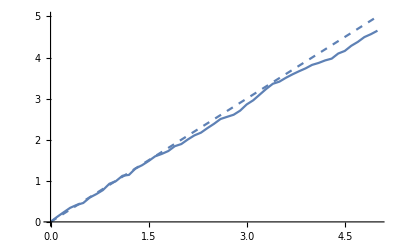

```mathematica
Show[Plot[Evaluate@Mean[𝒫[t]],{t,0,5},PlotStyle->Dashed],ListLinePlot[SliceTransform[Mean,data,Range[0,5,0.1]]]]
```

## Random Variables Obtained from Random Processes: Multivariate Examples

Multivariate slice distributions:

𝒫[{t_1,…,t_n}] or SliceDistribution[𝒫,{t_1,…,t_n}] is the joint distribution of {x[t_1,ω],…,x[t_n,ω]}.

Multivariate slices from random processes:

```mathematica
SliceDistribution[WienerProcess[μ,σ],{Subscript[t, 1],Subscript[t, 2]}]
```

BinormalDistribution[{μ t_1,μ t_2},{σ √t_1,σ √t_2},√(t_1/t_2)]

was

BinormalDistribution[{μ t_1,μ t_2},{σ √t_1,σ √t_2},Min[t_1,t_2]/(√(t_1 t_2))]

What happened to the Min operation, Min[t_1,t_2]

We can use random processes to generate multivariate random variables that have all the properties, such as probability values and simulated random variates:

```mathematica
𝒫=WienerProcess[1,1];
```

```mathematica
RandomVariate[𝒫[{1,2}],5]
```

{{-0.387402,1.78363},{0.0817379,2.17341},{-0.161428,1.11619},{0.715267,2.41574},{1.34644,4.98643}}

```mathematica
Probability[a<b,{a,b}\[Distributed]𝒫[{1,2}]]
```

1/2 (1+Erf[1/(√2)])

```mathematica
Probability[x[1]<x[2],x\[Distributed]𝒫]
```

1/2 (1+Erf[1/(√2)])

We can generate multivariate slices from data:

```mathematica
data=RandomFunction[𝒫,{0,10,0.1},1000];
```

```mathematica
data["SliceData",{1,2}]//Short
```

{{0.923593,0.610895},{1.22194,3.50077},«997»,{1.22526,-0.789879}}

And then compare the theoretical slice distribution of the process with the generated data:

```mathematica
Plot3D[Evaluate@PDF[𝒫[{1,2}],{x,y}],{x,-2,4},{y,-2,4}]
```

-Graphics3D-

```mathematica
SmoothHistogram3D[data["SliceData",{1,2}],PlotRange->{{-2,4},{-2,4},Automatic}]
```

-Graphics3D-

```mathematica
Clear[s,t]
```

We can calculate the absolute correlation function for the process at any two times s and t and create the resultant 3D plot:

```mathematica
AbsoluteCorrelationFunction[WienerProcess[μ,σ],s,t]
```

s t μ^2+σ^2 Min[s,t]

was

s t μ^2+σ^2 Min[s,t]

```mathematica
Plot3D[Evaluate@AbsoluteCorrelationFunction[WienerProcess[1,1],s,t],{s,0,10},{t,0,10}]
```

-Graphics3D-

## Time Series Processes

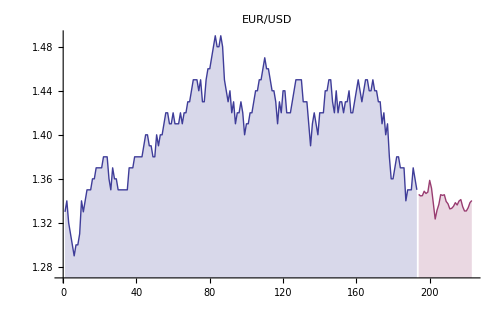

### Forecast exchange rates

The daily exchange rates of the euro to the dollar from May 2012 through September 2012:

```mathematica
FinancialData["EUR/USD"]
```

1.18332

```mathematica
FinancialData["EUR/USD",{{2012,5,1},{2012,9,30}}]
```

Missing[NotAvailable]

```mathematica
FinancialData[{"EUR","USD"},{{2012,5,1},{2012,9,30}}]
```

Missing[NotAvailable]

What happened to historical exchange rates. Should really be working.

```mathematica
FinancialData["USD",{{2012,5,1},{2012,9,30}}]
```

Missing[NotAvailable]

```mathematica
FinancialData["EUR",{{2012,5,1},{2012,9,30}}]
```

Missing[NotAvailable]

http://community.wolfram.com/groups/-/m/t/565781

How to get FinancialData[] Exchange Rates

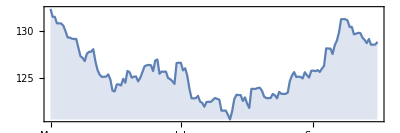

```mathematica
tmp=WolframAlpha["EUR vs USD from 2012/5/1 to 2012/10/1",{{"Result",1},"ComputableData"}];
DateListPlot[Most[tmp],PlotTheme->"Detailed",AspectRatio->1/3,Filling->Bottom]
```

```mathematica
tmp=Most[tmp];
```

```mathematica
data=TemporalData[tmp]["Part",All,{{2012,5,1},{2012,10,1}}]
```

TemporalData[…]

data = TemporalData[FinancialData["EUR/USD", {{2012, 5, 1}, {2012, 9, 30}}]]["Part", All, {{2012, 5, 1}, {2012, 9, 30}}];

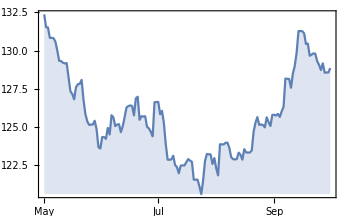

```mathematica
DateListPlot[data["Path"],Joined->True,Filling->Bottom,ImageSize->350]
```

Find parameters for an ARIMAProcess model:

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[40,2,0]]
```

ARIMAProcess[0.077345,{-0.800531,-0.779672,-0.702938,-0.695482,-0.600809,-0.589087,-0.464982,-0.407251,-0.376325,-0.215666,-0.343304,-0.390593,-0.323882,-0.267514,-0.270784,-0.126264,-0.192798,-0.0948171,-0.107079,-0.160029,-0.283381,-0.182471,-0.220474,-0.240924,-0.106025,-0.0648748,0.0804457,0.081094,0.065108,-0.0188825,-0.0306396,-0.0729696,-0.0604469,-0.137038,-0.0589935,-0.128069,-0.0236041,-0.0825312,-0.00140633,-0.00149232},2,{},0.298997]

was

ARIMAProcess[{-1.01508,-0.972494,-0.953972,-0.86005,-0.839793,-0.715588,-0.739701,-0.738409,-0.596945,-0.566367,-0.599522,-0.615074,-0.671958,-0.606196,-0.548357,-0.370722,-0.319851,-0.316957,-0.416449,-0.269208,-0.416906,-0.457057,-0.266016,-0.249609,-0.259942,-0.205678,-0.0931998,-0.0816428,-0.167612,-0.198906,-0.147454,-0.303037,-0.311317,-0.337149,-0.282161,-0.2739,-0.156258,-0.0398268,-0.0367763,-0.0581818},2,{},0.0000352388]

Forecast for 20 business days ahead:

```mathematica
forecast=TimeSeriesForecast[eproc,data,{20}]
```

TemporalData[…]

Plot the forecast with the original data:

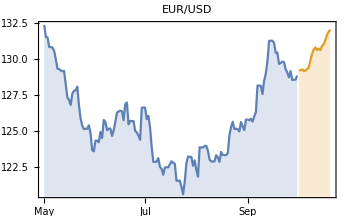

```mathematica
DateListPlot[{
data["Path"],
forecast["Path"]},
Joined->True,Filling->Axis,PlotLabel->"EUR/USD",ImageSize->350]
```

was

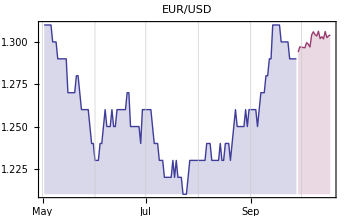

We should add the forecast with the actual data from the same extension

## Stochastic Differential Equation Processes

So how does one proceed from ODEs to SDEs? In this section, we shall look at how SDEs can be built up from ODEs and PDEs. The picture below graphically presents a random process description of a wave front where the collection of random paths when taken together corresponds to the associated PDE.

### Deterministic differential equations

First we consider the solution to a deterministic ODE:

```mathematica
With[{len=Function[1]},
NDSolveValue[{y''[t]+len[t]Sin[y[t]]==0,y[0]==Pi/3,y'[0]==0},y,{t,0,2Pi}]]
```

InterpolatingFunction[…]

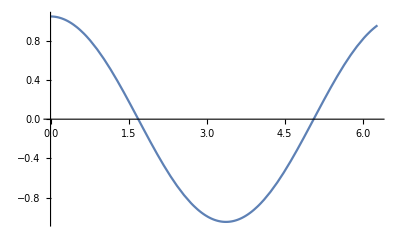

```mathematica
Plot[%[t],{t,0,2Pi}]
```

### Random distribution input

The above plot has no randomness, so we will add some noise from the normal distribution:

```mathematica
lenf[t_]=Evaluate[ 1+Table[(63/128)^k Sin[2^k t],{k,1,8}].RandomVariate[NormalDistribution[],8]]
```

1+0.552649 Sin[2 t]-0.222802 Sin[4 t]+0.0970496 Sin[8 t]+0.0476876 Sin[16 t]-0.000300092 Sin[32 t]+0.0158109 Sin[64 t]-0.000231657 Sin[128 t]-0.000823592 Sin[256 t]

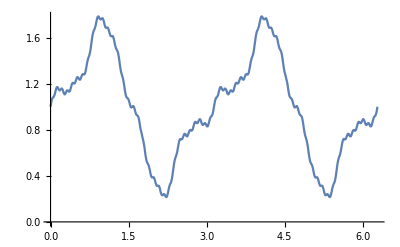

```mathematica
Plot[lenf[t],{t,0,2Pi},AxesOrigin->{0,0}]
```

```mathematica
{pos,vel}=With[{len=lenf},
NDSolveValue[{y''[t]+len[t]Sin[y[t]]==0,y[0]==Pi/3,y'[0]==0},{y,y'},{t,0,2Pi}]]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

Comparing the two plots:

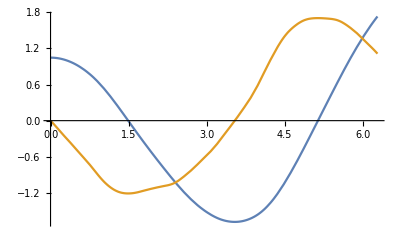

```mathematica
Plot[{pos[t],vel[t]},{t,0,2Pi}]
```

### Stochastic process input

The original deterministic DE can be rewritten as a system of first-order ODEs, and then we will add a white noise component:

y''[t]+ℓ[t] Sin[y[t]]==0 can be rewritten as a system of first-order ODEs

y'[t]==v[t], v'[t]==-ℓ[t]Sin[y[t]] or as

ⅆy[t]==v[t]ⅆt, ⅆv[t]==-ℓ[t] Sin[y[t]]ⅆt

Now consider -ℓ[t]ⅆt ==-ⅆt+1/2 ⅆw[t], that is, it has white noise component ⅆw[t]==𝓃[t]ⅆt.

The last pair of equations can be written as an ODE and an SDE using the function ItoProcess:

```mathematica
pr=ItoProcess[(* equations *)
{ⅆy[t]==v[t]ⅆt,ⅆv[t]==-Sin[y[t]]ⅆt+1/2 Sin[y[t]]ⅆw[t]},
y[t],(* output *)
{{y,v},{Pi/3,0}}, (* variables, and init. conds. *)
t,(* time origin *)
w\[Distributed]WienerProcess[] (* driving noise *)]
```

ItoProcess[{{v[t],-Sin[y[t]]},{{0},{1/2 Sin[y[t]]}},y[t]},{{y,v},{π/3,0}},{t,0}]

The resultant Ito process can be plotted and its mean and SD can be calculated at any time:

```mathematica
path=RandomFunction[pr,{0.,2.Pi,0.01},16]
```

TemporalData[16]

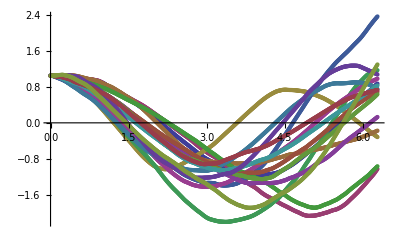

```mathematica
ListPlot[%]
```

```mathematica
path[0.5]
```

DataDistribution[«Empirical»,{16}]

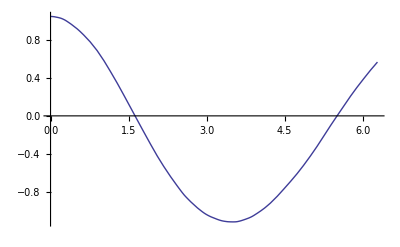

```mathematica
Plot[path[t]//Mean,{t,0,2Pi}]
```

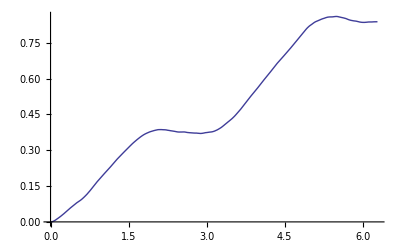

```mathematica
Plot[path[t]//StandardDeviation,{t,0,2Pi}]
```

## Examples of Ito Process and Its Outputs

Several special processes can be represented as an ItoProcess:

```mathematica
ItoProcess[WienerProcess[μ,σ]]
```

ItoProcess[{{μ},{{σ}},x[t]},{{x},{0}},{t,0}]

```mathematica
ItoProcess[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]]]
```

ItoProcess[{{μ x[t]},{{σ x[t]}},x[t]},{{x},{x_0}},{t,0}]

```mathematica
ItoProcess[OrnsteinUhlenbeckProcess[μ,σ,θ,Subscript[x, 0]]]
```

ItoProcess[{{θ (μ-x[t])},{{σ}},x[t]},{{x},{x_0}},{t,0}]

```mathematica
Mean[%[t]]//Expand
```

μ-ⅇ^(-t θ) μ+ⅇ^(-t θ) x_0

```mathematica
ItoProcess[CoxIngersollRossProcess[μ,σ,θ,Subscript[r, 0]]]
```

ItoProcess[{{θ (μ-x[t])},{{σ √x[t]}},x[t]},{{x},{r_0}},{t,0}]

```mathematica
ItoProcess[BrownianBridgeProcess[σ,{Subscript[t, 1],a},{Subscript[t, 2],b}]]
```

ItoProcess[{{(b-x[t])/(-t+t_2)},{{σ}},x[t]},{{x},{a}},{t,t_1}]

We can also represent Ito processes in terms of their generating SDEs:

```mathematica
ItoProcess[ⅆx[t]==(1/2-x[t])ⅆt+√(x[t](1-x[t]))ⅆw[t],x[t],{x,Subscript[x, 0]},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{1/2 (1-2 x[t])},{{√(-(-1+x[t]) x[t])}},x[t]},{{x},{x_0}},{t,0}]

Let b[t] be an Ito process and let y[t]==Exp[b[t]-t/2] be a function of b[t]; then y[t] is also an Ito process:

```mathematica
ItoProcess[ⅆb[t]==μⅆt+σ ⅆw[t],Exp[b[t]-μ t-σ^2 t/2],{b,0},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{μ},{{σ}},ⅇ^(-t μ-(t σ^2)/2+b[t])},{{b},{0}},{t,0}]

The process y[t] is also an Ito process:

```mathematica
ItoProcess[%]
```

ItoProcess[{{μ,0},{{σ},{ⅇ^(-t μ-(t σ^2)/2+b[t]) σ}},x$16024[t]},{{b,x$16024},{0,1}},{t,0}]

For the mapping y[t]==f[t,x[t]] to be an Ito process again, function f should be good enough (f∈𝒞^(1,2)):

```mathematica
ItoProcess[ⅆx[t]==a[t,x[t]]ⅆt+b[t,x[t]] ⅆw[t],f[t,x[t]],{x,x0},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{a[t,x[t]]},{{b[t,x[t]]}},f[t,x[t]]},{{x},{x0}},{t,0}]

The formula for drift and diffusion coefficients for Ito differentiation of y(t) in terms of f(t,x) and coefficients of x(t) is known as the Ito formula:

```mathematica
ItoProcess[%]//ExpandAll//TraditionalForm
```

ItoProcess[{{a(t,x(t)),a(t,x(t)) f^(0,1)(t,x(t))+1/2 (b(t,x(t)))^2 f^(0,2)(t,x(t))+f^(1,0)(t,x(t))},(b(t,x(t))
b(t,x(t)) f^(0,1)(t,x(t))),x$16067[t]},(x | x$16067
x0 | f(0,x0)),{t,0}]

## Simulation of Stochastic Processes

Stochastic processes can be manipulated symbolically and simulated:

```mathematica
pr=ItoProcess[{ⅆx[t]==(1-x[t]-y[t])ⅆt+ⅆw1[t],ⅆy[t]==-2x[t]ⅆt+ⅆw2[t]},{x[t],y[t]},{{x,y},{Subscript[x, 0],Subscript[y, 0]}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}]
```

ItoProcess[{{1-x[t]-y[t],-2 x[t]},{{1,0},{0,1}},{x[t],y[t]}},{{x,y},{x_0,y_0}},{t,0}]

```mathematica
npr=(pr/.{Subscript[x, 0]->1/2,Subscript[y, 0]->1/2})
```

ItoProcess[{{1-x[t]-y[t],-2 x[t]},{{1,0},{0,1}},{x[t],y[t]}},{{x,y},{1/2,1/2}},{t,0}]

```mathematica
RandomFunction[npr,{0,5,0.01},20]
```

TemporalData[20]

```mathematica
Mean[npr[5]]
```

{(1+2 ⅇ^15)/(6 ⅇ^10),1/6 (6+1/ⅇ^10-4 ⅇ^5)}

```mathematica
N[%]
```

{49.4711,-97.9421}

```mathematica
PDF[npr[5],{x,y}]//Simplify
```

(3 ⅇ^((-106-5 x^2+10 x (-1+y)+10 y-5 y^2+ⅇ^25 (91-16 x^2-16 x (-1+y)+8 y-4 y^2)-ⅇ^5 (100+5 x^2+x (4-10 y)-4 y+5 y^2)+ⅇ^15 (-92+11 x^2+20 y-13 y^2+2 x (8+y))+ⅇ^10 (80-5 x^2+4 y-5 y^2+2 x (4+5 y))-ⅇ^20 (-109+16 x^2+10 y+4 y^2+2 x (-5+8 y)))/(2 (-1+ⅇ^5) (5+10 ⅇ^5+6 ⅇ^10+10 ⅇ^15+5 ⅇ^20))))/((-1+ⅇ^5) √(5+10 ⅇ^5+6 ⅇ^10+10 ⅇ^15+5 ⅇ^20) π)

```mathematica
RandomFunction[npr,{0,5,0.01},20,Method->"Milstein"]
```

TemporalData[20]

```mathematica
Mean[%[5]]
```

{51.4787,-101.99}

Simulate the process ⅆx[t]==-x[t]ⅆt+σ ⅆw[t]:

```mathematica
Manipulate[
proc=ItoProcess[ⅆx[t]==-x[t]ⅆt+σⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]];
ListLinePlot[RandomFunction[proc,{0.,10,0.05},10],PlotRange->{-0.5,1.5}],
{{σ,0.05},0.,0.5},SaveDefinitions->True]
```

For some processes we can compute properties symbolically:

```mathematica
𝒫=ItoProcess[ⅆx[t]==-x[t]ⅆt+1/10ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]];
```

```mathematica
m=Mean[𝒫[t]]
```

ⅇ^-t

```mathematica
v=Variance[𝒫[t]]
```

1/200 ⅇ^(-2 t) (-1+ⅇ^(2 t))

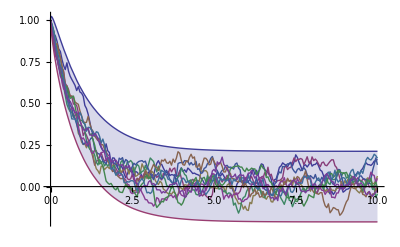

```mathematica
Show[
ListLinePlot[RandomFunction[𝒫,{0,10,0.05},10],PlotRange->All],
Plot[{m+3 √v,m-3 √v},{t,0,10},Filling->{1->{2}}]]
```

Even the slice distributions:

```mathematica
𝒫=ItoProcess[ⅆx[t]==-x[t]ⅆt+1/10ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]];
```

```mathematica
pdf=PDF[𝒫[t],x]
```

(10 ⅇ^(-(100 ⅇ^t (-ⅇ^-t+x) (-1+ⅇ^t x))/(-1+ⅇ^(2 t))))/(√(ⅇ^(-2 t) (-1+ⅇ^(2 t))) √π)

```mathematica
Plot3D[pdf,{x,-0.2,1},{t,0,10},PlotPoints->50,AxesLabel->Automatic,PlotRange->{0,6}]
```

-Graphics3D-

## Financial Functions: Geometric Brownian Motion Process

The famous Black-Scholes model for daily stock prices is built upon the notion that such prices behave like geometric Brownian motion. It is because this process when viewed at any fixed time t has the properties of the LogNormal distribution that they were able to integrate values to solve for any option or random function of the LogNormal distribution.

Mean and variance functions:

```mathematica
Mean[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]][t]]//Simplify
```

ⅇ^(t μ) x_0

```mathematica
Variance[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]][t]]//Simplify
```

ⅇ^(2 t μ) (-1+ⅇ^(t σ^2)) x_0^2

Covariance function:

```mathematica
CovarianceFunction[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]],s,t]
```

ⅇ^((s+t) μ) (-1+ⅇ^(σ^2 Min[s,t])) x_0^2

GeometricBrownianMotionProcess is not weakly stationary:

```mathematica
WeakStationarity[GeometricBrownianMotionProcess[μ,σ,a]]
```

False

Univariate time slice follows a LogNormalDistribution:

```mathematica
GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]][t]
```

LogNormalDistribution[t (μ-σ^2/2)+Log[x_0],√t σ]

Multi-time slice follows a LogMultinormalDistribution:

```mathematica
GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]][{1,2}]
```

LogMultinormalDistribution[{μ-σ^2/2+Log[x_0],2 (μ-σ^2/2)+Log[x_0]},{{σ^2,σ^2},{σ^2,2 σ^2}}]

A geometric Brownian motion process is a special ItoProcess:

```mathematica
ItoProcess[GeometricBrownianMotionProcess[μ,σ,a]]
```

ItoProcess[{{μ x[t]},{{σ x[t]}},x[t]},{{x},{a}},{t,0}]

As well as StratonovichProcess:

```mathematica
StratonovichProcess[GeometricBrownianMotionProcess[μ,σ,a]]
```

StratonovichProcess[{{(μ-σ^2/2) x[t]},{{σ x[t]}},x[t]},{{x},{a}},{t,0}]

Correlation function:

```mathematica
CorrelationFunction[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]],s,t]
```

(-1+ⅇ^(σ^2 Min[s,t]))/(√(-1+ⅇ^(s σ^2)) √(-1+ⅇ^(t σ^2)))

First-order probability density function:

```mathematica
PDF[GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]][t],x]
```

Piecewise[{{(ⅇ^(-((-t (μ-σ^2/2)+Log[x]-Log[x_0])^2)/(2 t σ^2)))/(√(2 π) √t x σ), x>0}, {0, True}}]

Compute an expectation:

```mathematica
Expectation[x[t]^2,x\[Distributed]GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]]]
```

ⅇ^(2 t σ^2+2 t (μ-σ^2/2)) x_0^2

Calculate the probability of an event:

```mathematica
Probability[x[t]<1,x\[Distributed]GeometricBrownianMotionProcess[μ,σ,Subscript[x, 0]]]
```

1/2 Erfc[(t (μ-σ^2/2)+Log[x_0])/(√2 √t σ)]

#### Actual daily financial data

```mathematica
fdata=FinancialData["SP500",DatePlus[-360]];
```

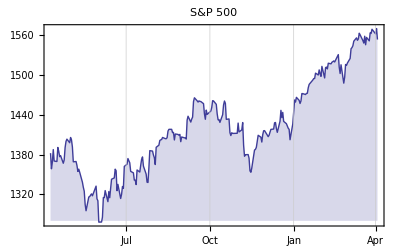

```mathematica
DateListPlot[fdata,PlotLabel->"S&P 500",Joined->True, Filling->Axis]
```

```mathematica
fvalues=Transpose[{Range[0,Length[fdata]-1],Transpose[fdata][[2]]}];
```

```mathematica
eproc=EstimatedProcess[fvalues,GeometricBrownianMotionProcess[μ,σ,x]]
```

GeometricBrownianMotionProcess[0.000508394,0.0081194,1382.2]

```mathematica
sims=RandomFunction[eproc,{0,Length[fdata]-1,1},10]
```

TemporalData[10]

```mathematica
Length[sims["Paths"]]
```

10

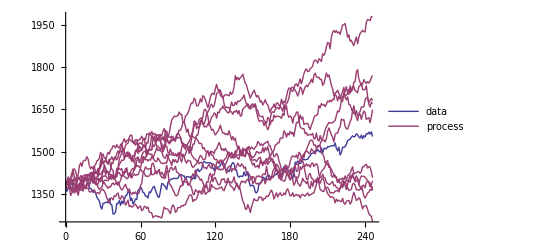

```mathematica
ListLinePlot[Join[{fvalues},sims["Paths"]],PlotStyle->Prepend[Table[ColorData[1,2],{Length[sims["Paths"]]+1}],Directive[Thick,ColorData[1,1]]],PlotLegends->{"data","process"}]
```

## One-Factor, Short-Interest-Rate Models

In all of the cases below, we give the SDE definition of the interest rate process, then its corresponding built-in Finance Platform definition, show that they are the same, and plot multiple paths.

### Merton's model (1973)

Merton’s model ⅆr(t)==μⅆt+σ ⅆw(t) is the Wiener process with nonzero drift μ and diffusion σ, and nonzero initial value r_0:

```mathematica
ItoProcess[WienerProcess[μ,σ]]
```

ItoProcess[{{μ},{{σ}},x[t]},{{x},{0}},{t,0}]

Use differential notation ⅆr(t)==μ ⅆt+σ ⅆw(t) with initial condition r(0)=r_0 to define the same process:

```mathematica
ItoProcess[ⅆr[t]==μ ⅆt+σ ⅆw[t],r[t],{r,Subscript[r, 0]},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{μ},{{σ}},r[t]},{{r},{r_0}},{t,0}]

This is equivalent to a simple Ito process with initial conditions:

```mathematica
ItoProcess[{μ,σ},{r,Subscript[r, 0]},t]
```

ItoProcess[{{μ},{{σ}},r[t]},{{r},{r_0}},{t,0}]

```mathematica
merton[μ_,σ_,r0_]=ItoProcess[{μ,σ,r[t]},{r,r0},t]
```

ItoProcess[{{μ},{{σ}},r[t]},{{r},{r0}},{t,0}]

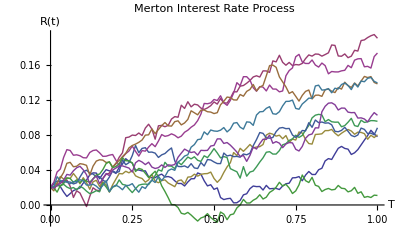

```mathematica
ListLinePlot[#,AxesLabel->{"T","R(t)"},PlotLabel->"Merton Interest Rate Process"]& @RandomFunction[merton[0.1,0.05,0.02],{0.,1.,0.01},10,Method->"Milstein"]
```

### Vasicek model (1977)

Vasicek’s model ⅆr(t)==θ (μ-r(t))ⅆt+σ ⅆw(t) is the Ornstein-Uhlenbeck process with nonzero long-term mean μ and volatility σ, mean reversion rate θ, and nonzero initial value r_0:

```mathematica
ItoProcess[ⅆr[t]==θ(μ -r[t])ⅆt+σ ⅆw[t],r[t],{r,Subscript[r, 0]},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{θ μ-θ r[t]},{{σ}},r[t]},{{r},{r_0}},{t,0}]

```mathematica
ItoProcess[OrnsteinUhlenbeckProcess[μ,σ,θ,Subscript[r, 0]]]
```

ItoProcess[{{θ (μ-x[t])},{{σ}},x[t]},{{x},{r_0}},{t,0}]

```mathematica
vasicek[μ_,σ_,θ_,r0_]=OrnsteinUhlenbeckProcess[μ,σ,θ,r0]
```

OrnsteinUhlenbeckProcess[μ,σ,θ,r0]

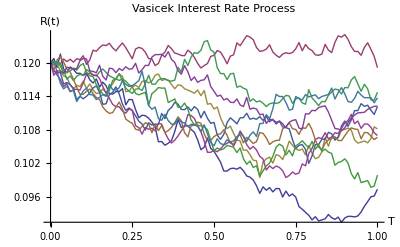

```mathematica
ListLinePlot[#,AxesLabel->{"T","R(t)"},PlotLabel->"Vasicek Interest Rate Process"]& @RandomFunction[vasicek[0.1,0.01,1.5,0.12],{0.,1.,0.01},10]
```

### Rendleman-Bartter model (1980)

The Rendleman-Bartter model ⅆr(t)==θ r(t)ⅆt+σ r(t) ⅆw(t) is the geometric Brownian motion process with nonzero drift θ, volatility σ, and nonzero initial value r_0:

```mathematica
ItoProcess[ⅆr[t]==θ r[t] ⅆt+σ r[t] ⅆw[t],r[t],{r,Subscript[r, 0]},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{θ r[t]},{{σ r[t]}},r[t]},{{r},{r_0}},{t,0}]

```mathematica
ItoProcess[GeometricBrownianMotionProcess[θ,σ,Subscript[r, 0]]]
```

ItoProcess[{{θ x[t]},{{σ x[t]}},x[t]},{{x},{r_0}},{t,0}]

```mathematica
rendlemanBarter[θ_,σ_,r0_]=GeometricBrownianMotionProcess[θ,σ,r0]
```

GeometricBrownianMotionProcess[θ,σ,r0]

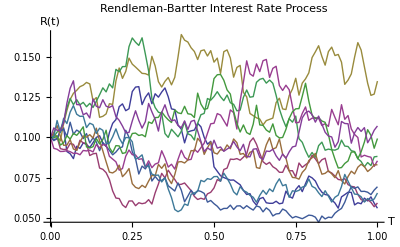

```mathematica
ListLinePlot[#,AxesLabel->{"T","R(t)"},PlotLabel->"Rendleman-Bartter Interest Rate Process"]& @RandomFunction[rendlemanBarter[0.2,0.5,0.1],{0.,1.,0.01},10]
```

### Cox-Ingersoll-Ross model (1985)

The Cox–Ingersoll–Ross model ⅆr(t)==θ (μ-x(t))ⅆt+σ √(x(t)) ⅆw(t) with long-term mean μ, volatility σ, speed of adjustment θ, and initial condition r_0:

```mathematica
ItoProcess[ⅆr[t]==θ(μ -r[t]) ⅆt+σ √r[t] ⅆw[t],r[t],{r,Subscript[r, 0]},t,w\[Distributed]WienerProcess[]]
```

ItoProcess[{{θ μ-θ r[t]},{{σ √r[t]}},r[t]},{{r},{r_0}},{t,0}]

CoxIngersollRossProcess[μ,σ,θ,r_0] represents a Cox–Ingersoll–Ross process with long-term mean μ, volatility σ, speed of adjustment θ, and initial condition r_0:

```mathematica
ItoProcess[CoxIngersollRossProcess[μ,σ,θ,Subscript[r, 0]]]
```

ItoProcess[{{θ (μ-x[t])},{{σ √x[t]}},x[t]},{{x},{r_0}},{t,0}]

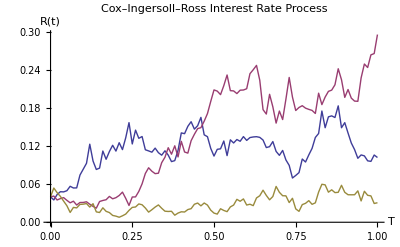

```mathematica
ListLinePlot[#,AxesLabel->{"T","R(t)"},PlotLabel->"Cox–Ingersoll–Ross Interest Rate Process"]& @ParallelTable[RandomFunction[CoxIngersollRossProcess[0.03,0.4,0.3,0.04],{0.,1.,0.01}],{3}]
```

## Code

#### Display Boxes

CellDisplay: print cell without Out[nn]

```mathematica
CellDisplay[expr_]:=CellPrint[ExpressionCell[expr,"Output",Background->None,ShowCellLabel->False,CellFrame->False,CellMargins->{{100,100},{40,0}}]]
```

FrameDisplay: frame object with standard settings for this document

```mathematica
FrameDisplay[expr_]:=Framed[expr,RoundingRadius->10,Background->Lighter[Gray,0.9],FrameMargins->10,FrameStyle->GrayLevel[0.5]]
```

A grid of definitions:

```mathematica
ProcessDefinitionGrid[{{duv_,dmv_},{cuv_,cmv_}}]:=
FrameDisplay@Grid[
{{SpanFromLeft,Text[Style["Discrete State",FontFamily->"Helvetica"]],Text[Style["Continuous State",FontFamily->"Helvetica"]]},
{Text[Style["Discrete Time",FontFamily->"Helvetica"]],TraditionalForm@duv,TraditionalForm@dmv},
{Text[Style["Continuous Time",FontFamily->"Helvetica"]],TraditionalForm@cuv,TraditionalForm@cmv}},
Spacings->{2,4},
Dividers->{{False,True,True,False},{False,True,True,False}}
]
```

```mathematica
FormattedDefinitionGrid[{{duv_,dmv_},{cuv_,cmv_}}]:=
FrameDisplay@Style[Grid[
{{SpanFromLeft,Text[Style["Univariate",FontFamily->"Helvetica"]],Text[Style["Multivariate",FontFamily->"Helvetica"]]},
{Text[Style["Discrete",FontFamily->"Helvetica"]],duv,dmv},
{Text[Style["Continuous",FontFamily->"Helvetica"]],cuv,cmv}},
Spacings->{2,4},
Dividers->{{False,True,True,False},{False,True,True,False}}
],"Text"]
```

A grid of lists:

```mathematica
PaneList[list_]:=
Pane[Style[Column[list⟦1;;-1⟧],"Text"],300]
```

```mathematica
ProcessListGrid[{{duv_,dmv_},{cuv_,cmv_}}]:=
FrameDisplay@Grid[
{{SpanFromLeft,Text[Style["Discrete State",FontFamily->"Helvetica"]],Text[Style["Continuous State",FontFamily->"Helvetica"]]},
{Text[Style["Discrete Time",FontFamily->"Helvetica"]],PaneList@duv,PaneList@dmv},
{Text[Style["Continuous Time",FontFamily->"Helvetica"]],PaneList@cuv,PaneList@cmv}},
Spacings->{2,4},
Dividers->{{False,True,True,False},{False,True,True,False}}
]
```

#### EventMatrixPlot

```mathematica
EventMatrixPlot[data_EventData]:=SurvivalModelFit[data]["EventMatrixPlot"]
```

#### DistributionPlot (Univariate)

Notes/Todos:

• Various checks, messages, and graceful failures. 
• Filter options that go to Plot and DiscretePlot. 
• Add additional properties (e.g. confidence region) to visualize together with these.

Plot Domain Automation:

• supportDomain: range over which distribution functions have non-zero support.

```mathematica
supportDomain[dist_]/;Statistics`Library`DiscreteUnivariateDistributionQ[dist]:=
Module[{dom=DistributionDomain[dist]},If[Head[dom]===Range,List@@dom,{First[dom],Last[dom]}]]
```

```mathematica
supportDomain[dist_]/;Statistics`Library`ContinuousUnivariateDistributionQ[dist]:=
Module[{dom=DistributionDomain[dist]},First[dom]]
```

• quantileDomain: the domain {Q[p_min],Q[p_max]} which contain p_max-p_min fraction of the weight of the distribution.

```mathematica
quantileDomain[dist_,{qmin_,qmax_}]/;Statistics`Library`UnivariateDistributionQ[dist]:=Quantile[dist,{qmin,qmax}]
```

```mathematica
quantileDomain[dist_,q_]:=quantileDomain[dist,{(1-q)/2,q+(1-q)/2}]
```

• automaticDomain: might have to include additional logic for heavy-tailed distributions (for now just tone down the quantile)
 - could consider quantile domain for p q^i and

```mathematica
automaticDomain[dist_,p_:0.99]/;Statistics`Library`UnivariateDistributionQ[dist]:=
Module[{sdom,qdom,q=0.9},
sdom=supportDomain[dist];
qdom=Which[NumericQ[Moment[dist,2]],quantileDomain[dist,p],NumericQ[Moment[dist,1]],quantileDomain[dist,p q],True,quantileDomain[dist,p q^2]];
automaticDomainLogic[sdom,qdom]
];
```

```mathematica
automaticDomainLogic[{sxmin_,sxmax_},{qxmin_,qxmax_}]:=
Module[{α=3,β=2},
Switch[{sxmin,sxmax},
{-Infinity,Infinity},{qxmin,qxmax},
{-Infinity,_},If[(sxmax-qxmin)>α(qxmax-qxmin),{qxmin,qxmax},{qxmin,sxmax}],
{_,Infinity},If[(qxmax-sxmin)>α(qxmax-qxmin),{qxmin,qxmax},{sxmin,qxmax}],
{_,_},If[(sxmax-sxmin)>β(qxmax-qxmin),{qxmin,qxmax},{sxmin,sxmax}]
]
]
```

DistributionPlot:

```mathematica
DistributionPlot[dist_,o:OptionsPattern[]]:=DistributionPlot[dist,Automatic,"PDF",o]
```

```mathematica
DistributionPlot[dist_,dom_,o:OptionsPattern[]]:=DistributionPlot[dist,dom,"PDF",o]
```

```mathematica
DistributionPlot[dist_,dom_,type_String,o:OptionsPattern[]]:=
Catch@Module[{xmin,xmax,f},
(* Domain and Type *)
{xmin,xmax}=Which[dom===Automatic,automaticDomain[dist],True,dom];
f=Switch[type,"PDF",PDF,"CDF",CDF,"SF",SurvivalFunction,"HF",HazardFunction,True,Throw[$Failed]];
(* Discrete/Continuous *)
Which[
Statistics`Library`ContinuousUnivariateDistributionQ[dist],continuousDistributionPlot[dist,{xmin,xmax},f,o],
Statistics`Library`DiscreteUnivariateDistributionQ[dist],discreteDistributionPlot[dist,{xmin,xmax},f,o],
True,$Failed
]
]
```

```mathematica
discreteDistributionPlot[dist_,{xmin_,xmax_},f:(PDF|HazardFunction),o:OptionsPattern[]]:=
DiscretePlot[Evaluate[f[dist,x]],{x,Ceiling[xmin],Floor[xmax]},o,ExtentSize->1/2,PlotRange->{All,{0,Automatic}}]
```

```mathematica
discreteDistributionPlot[dist_,{xmin_,xmax_},f:(CDF|SurvivalFunction),o:OptionsPattern[]]:=
DiscretePlot[Evaluate[f[dist,x]],{x,Ceiling[xmin],Floor[xmax]},o,ExtentSize->Right,PlotRange->{All,{0,Automatic}}]
```

```mathematica
continuousDistributionPlot[dist_,{xmin_,xmax_},f:(PDF|CDF|SurvivalFunction|HazardFunction),o:OptionsPattern[]]:=
Plot[Evaluate[f[dist,x]],{x,xmin,xmax},o,Filling->Axis,PlotRange->{0,Automatic}]
```

#### DistributionPlot3D (Bivariate)

Notes/Todos:

• Various checks and messages for graceful failures and recovery. 
• Filter options that go to Plot3D and DiscretePlot3D. 
• Additional property visualization such as marginal distribution functions, confidence regions etc.

Utilities:

```mathematica
BivariateContinuousDistributionQ[dist_]:=Statistics`Library`ContinuousMultivariateDistributionQ[dist]&&Statistics`Library`DistributionDimensionality[dist]==2
```

```mathematica
BivariateDiscreteDistributionQ[dist_]:=Statistics`Library`DiscreteMultivariateDistributionQ[dist]&&Statistics`Library`DistributionDimensionality[dist]==2
```

```mathematica
BivariateDistributionQ[dist_]:=BivariateContinuousDistributionQ[dist]||BivariateDiscreteDistributionQ[dist]
```

Plot Domain Automation:

• supportDomain: range over which distribution functions have non-zero support. 
• quantileDomain: the domain {Q[p_min],Q[p_max]} which contain p_max-p_min fraction of the weight of the distribution. 
• automaticDomain: might have to include additional logic for heavy-tailed distributions

```mathematica
supportDomain[dist_]/;BivariateDiscreteDistributionQ[dist]:=
Module[{dom=DistributionDomain[dist]},Map[If[Head[#]===Range,List@@#,{First[#],Last[#]}]&,dom]]
```

```mathematica
supportDomain[dist_]/;BivariateContinuousDistributionQ[dist]:=
Module[{dom=DistributionDomain[dist]},Map[First,dom]]
```

```mathematica
quantileDomain[dist_,{qmin_,qmax_}]/;BivariateDistributionQ[dist]:=
Map[Quantile[#,{qmin,qmax}]&,Table[MarginalDistribution[dist,i],{i,2}]]
```

```mathematica
automaticDomain[dist_,p_:0.99]/;BivariateDistributionQ[dist]:=
MapThread[automaticDomainLogic,{supportDomain[dist],quantileDomain[dist,p]}]
```

DistributionPlot3D:

```mathematica
DistributionPlot3D[dist_,o:OptionsPattern[]]:=DistributionPlot3D[dist,Automatic,"PDF",o]
```

```mathematica
DistributionPlot3D[dist_,dom_,o:OptionsPattern[]]:=DistributionPlot3D[dist,dom,"PDF",o]
```

```mathematica
DistributionPlot3D[dist_,dom_,type_String,o:OptionsPattern[]]/;BivariateDistributionQ[dist]:=
Catch@Module[{xdom,ydom,f},
(* Domain and Type *)
{xdom,ydom}=Which[dom===Automatic,automaticDomain[dist],True,dom];
f=Switch[type,"PDF",PDF,"CDF",CDF,"SF",SurvivalFunction,"HF",HazardFunction];
(* Discrete/Continuous *)
Which[
BivariateContinuousDistributionQ[dist],continuousDistributionPlot3D[dist,{xdom,ydom},f,o],
BivariateDiscreteDistributionQ[dist],discreteDistributionPlot3D[dist,{xdom,ydom},f,o],
True,$Failed
]
]
```

```mathematica
discreteDistributionPlot3D[dist_,{xdom_,ydom_},f:(PDF|HazardFunction),o:OptionsPattern[]]:=
DiscretePlot3D[f[dist,{x,y}],{x,Ceiling[xdom⟦1⟧],Floor[xdom⟦2⟧]},{y,Ceiling[ydom⟦1⟧],Floor[ydom⟦2⟧]},o,ExtentSize->1/2]
```

```mathematica
discreteDistributionPlot3D[dist_,{xdom_,ydom_},f:(CDF|SurvivalFunction),o:OptionsPattern[]]:=
DiscretePlot3D[f[dist,{x,y}],{x,Ceiling[xdom⟦1⟧],Floor[xdom⟦2⟧]},{y,Ceiling[ydom⟦1⟧],Floor[ydom⟦2⟧]},o,ExtentSize->Right]
```

```mathematica
continuousDistributionPlot3D[dist_,{xdom_,ydom_},f:(PDF|CDF|SurvivalFunction|HazardFunction),o:OptionsPattern[]]:=
Plot3D[f[dist,{x,y}],{x,xdom⟦1⟧,xdom⟦2⟧},{y,ydom⟦1⟧,ydom⟦2⟧},o,MeshFunctions->{#3&}]
```

#### ListDiscretePlot

ListDiscretePlot:

```mathematica
Options[ListDiscretePlot]=Options[DiscretePlot];
```

```mathematica
ListDiscretePlot[data_,o:OptionsPattern[]]/;MatrixQ[data]:=
Module[{f=Interpolation[data,InterpolationOrder->1]},
DiscretePlot[f[t],{t,First/@data},o]
]
```

```mathematica
ListDiscretePlot[data_,o:OptionsPattern[]]:=
Show[Table[ListDiscretePlot[data⟦i⟧,o,PlotStyle->ColorData[1,i]],{i,Length[data]}]]
```

#### SliceDistribution

SliceDistribution: Automatic simplification: (these should all be a standard part ... and many more)

```mathematica
Unprotect[SliceDistribution]
```

{SliceDistribution}

```mathematica
SliceDistribution[WienerProcess[μ_,σ_],t_List]/;VectorQ[t,NumericQ]:=
Module[{tl=Sort[t]},MultinormalDistribution[μ tl,σ^2 Table[tl⟦Min[i,j]⟧,{i,Length[tl]},{j,Length[tl]}]]];
```

```mathematica
SliceDistribution[WienerProcess[μ_,σ_],t_List]:=
Module[{tl=t},MultinormalDistribution[μ tl,σ^2 Table[tl⟦Min[i,j]⟧,{i,Length[tl]},{j,Length[tl]}]]];
```

```mathematica
Protect[SliceDistribution]
```

{SliceDistribution}

```mathematica
SliceDistribution[BernoulliProcess[p],t]
```

BernoulliDistribution[p]

```mathematica
SliceDistribution[WienerProcess[μ,σ],t]
```

NormalDistribution[t μ,√t σ]

```mathematica
SliceDistribution[WienerProcess[μ,σ],{Subscript[t, 1],Subscript[t, 2]}]
```

BinormalDistribution[{μ t_1,μ t_2},{σ √t_1,σ √t_2},√(t_1/t_2)]

```mathematica
With[{tl={Subscript[t, 1],Subscript[t, 2]}},MultinormalDistribution[μ tl,σ^2 Table[tl⟦Min[i,j]⟧,{i,Length[tl]},{j,Length[tl]}]]]
```

MultinormalDistribution[{μ t_1,μ t_2},{{σ^2 t_1,σ^2 t_1},{σ^2 t_1,σ^2 t_2}}]

#### SliceDistributionPlot

SliceDistributionPlot:

```mathematica
iDistributionElement[{{xmin_,xmax_},{ymin_,ymax_}},data_,meta_]:=
Catch@Module[{g,sxmin,sxmax,symin,symax,dist,f},
{dist,f}=First@meta;
g=DistributionPlot[dist ,{xmin,xmax},f];
{{sxmin,sxmax},{symin,symax}}=ReplaceAll[PlotRange,Options[g,PlotRange]]; (* This may fail *)
GeometricTransformation[First[g],RescalingTransform[{{sxmin,sxmax},{symin,symax}},{{xmin,xmax},{ymin,ymax}}]]
]
```

```mathematica
iSliceDistributionPlot[dists_List,tl_List,f_:"PDF",o:OptionsPattern[]]:=
DistributionChart[Table[automaticDomain[dists⟦i⟧]->{dists⟦i⟧,f},{i,Length[dists]}],
BarOrigin->Left,
o,
ChartElementFunction->iDistributionElement,
ChartLabels->tl
]
```

```mathematica
SliceDistributionPlot[proc_,tl_List,f_:"PDF",o:OptionsPattern[]]:=
iSliceDistributionPlot[Table[SliceDistribution[proc,tl⟦i⟧],{i,Length[tl]}],tl,f,o]
```

#### SliceSmoothHistogram

SliceData:

```mathematica
(*Options[SliceData]={InterpolationOrder->1};
SliceData[path_List,tl_List,OptionsPattern[]]/;ArrayDepth[path]==2:=
Interpolation[path,InterpolationOrder->OptionValue[InterpolationOrder]][tl]
SliceData[paths_List,tl_List,OptionsPattern[]]/;And@@Table[ArrayDepth[paths⟦i⟧]==2,{i,Length[paths]}]:=
Transpose@Map[Interpolation[#,InterpolationOrder->OptionValue[InterpolationOrder]][tl]&,paths]*)
```

SliceMap:

```mathematica
SliceMap[f_,data_,tl_List]:=Map[f,Transpose@(data["SliceData",tl])]
```

SliceTransform:

```mathematica
SliceTransform[f_,data_,tl_List]:=TemporalData[SliceMap[f,data,tl],{tl}]
```

SliceSmoothHistogram: This is pretty much trivial with our building blocks.

```mathematica
SliceSmoothHistogram[data_,tl_List,o:OptionsPattern[]]:=
DistributionChart[SliceData[data,tl],o,BarOrigin->Left,ChartLabels->tl,ChartElementFunction-> ChartElementData["SmoothDensity","Shape"->"SingleSided"]]
```

#### $Line

```mathematica
$Line=0;
```

#### GetYahooMultiQuote

https://mathematica.stackexchange.com/questions/46760/how-to-request-financial-data-from-yahoos-yql-and-quandl

```mathematica
toYahooString[string_String]:="\""<>string<>"\"";
toYahooDate[date_List]:=DateString[date,{"Year","-","Month","-","Day"}]//toYahooString;
toYahooList[list_List]:=StringJoin@@Riffle[toYahooString/@list,","];
toYahooUrl[sqlRequest_String]:=Module[{urlRules},
urlRules={" "->"%20","\""->"%22","("->"%28",")"->"%29"};
StringReplace["http://query.yahooapis.com/v1/public/yql?env=store://datatables.org/alltableswithkeys&format=json&q="<>sqlRequest,urlRules]
];
toYahooRequest[sqlRequest_]:=sqlRequest//toYahooUrl//Import[#,"JSON"]&;
doAndParseYahooRequest[sqlRequest_,yahooResultField_,requiredFields_,nsymbols_]:=Module[{jsonImport,quotes},
jsonImport=sqlRequest//toYahooRequest;
quotes=OptionValue[jsonImport,yahooResultField];
requiredFields/.quotes//Partition[#,Length@#/nsymbols]&//If[Length@#==1,First@#,#]&];

possibleQuotes=Alternatives@@{"Adj_Close","Close","Date","High","Low","Open","Symbol","Volume"};

ClearAll@GetYahooMultiQuote;
GetYahooMultiQuote[symbols_,startDate_,endDate_,quote:(possibleQuotes|{possibleQuotes..}):"Adj_Close"]:=Module[{symbols2=Flatten@{symbols},sqlRequest,sqlRequestModified},sqlRequest="select * from yahoo.finance.historicaldata where symbol in (SYMBOLS) and startDate = START_DATE and endDate = END_DATE";
sqlRequestModified=StringReplace[sqlRequest,{"SYMBOLS"->toYahooList@symbols2,"START_DATE"->toYahooDate@startDate,"END_DATE"->toYahooDate@endDate}];
doAndParseYahooRequest[sqlRequestModified,"query"->"results"->"quote",quote,Length@symbols2]];
```

```mathematica
symbol="YHOO";
symbols={"YHOO","GE"};
startDate={2013,04,13};
endDate={2014,04,16};
```

```mathematica
sqlRequest="select * from yahoo.finance.historicaldata where symbol in (SYMBOLS) and startDate = START_DATE and endDate = END_DATE";
```

```mathematica
toYahooList@{"YHOO"}
```

"YHOO"

```mathematica
sqlRequestModified=StringReplace[sqlRequest,{"SYMBOLS"->toYahooList@{"YHOO"},"START_DATE"->toYahooDate@startDate,"END_DATE"->toYahooDate@endDate}]
```

select * from yahoo.finance.historicaldata where symbol in ("YHOO") and startDate = "2013-04-13" and endDate = "2014-04-16"

```mathematica
StringReplace["http://query.yahooapis.com/v1/public/yql?env=store://datatables.org/alltableswithkeys&format=json&q="<>sqlRequestModified,{" "->"%20","\""->"%22","("->"%28",")"->"%29"}]
```

http://query.yahooapis.com/v1/public/yql?env=store://datatables.org/alltableswithkeys&format=json&q=select%20*%20from%20yahoo.finance.historicaldata%20where%20symbol%20in%20%28%22YHOO%22%29%20and%20startDate%20=%20%222013-04-13%22%20and%20endDate%20=%20%222014-04-16%22

```mathematica
toYahooUrl[sqlRequestModified]
```

http://query.yahooapis.com/v1/public/yql?env=store://datatables.org/alltableswithkeys&format=json&q=select%20*%20from%20yahoo.finance.historicaldata%20where%20symbol%20in%20%28%22YHOO%22%29%20and%20startDate%20=%20%222013-04-13%22%20and%20endDate%20=%20%222014-04-16%22

```mathematica
Import[toYahooUrl[sqlRequestModified],"JSON"]
```

{query→{lang→en-US,count→0,created→2017-12-06T07:56:22Z,results→Null}}

That is how you end up with Results Null

```mathematica
GetYahooMultiQuote[symbol,startDate,endDate]
```

OptionValue::rep: Null is not a valid replacement rule.

OptionValue::optnf: Option name query→results→quote not found in defaults for {query→{lang→en-US,count→0,created→2017-12-06T07:36:00Z,results→Null}}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Adj_Close,0].

Partition[Adj_Close,0]

```mathematica
GetYahooMultiQuote[symbols,startDate,endDate,{"Adj_Close","High"}]
```

OptionValue::rep: Null is not a valid replacement rule.

OptionValue::optnf: Option name query→results→quote not found in defaults for {query→{lang→en-US,count→0,created→2017-12-06T07:36:06Z,results→Null}}.

{{Adj_Close},{High}}

https://www.wolfram.com/mathematica/new-in-10/dimensional-variables/convert-currencies-using-historical-exchange-rates.html